# One-dimensional plots

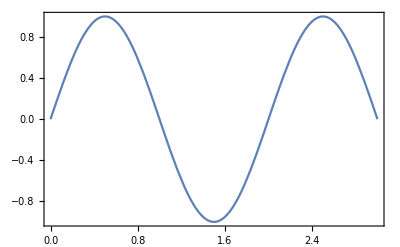

```mathematica
Plot[Sin[Pi x],{x,0,3}]
```

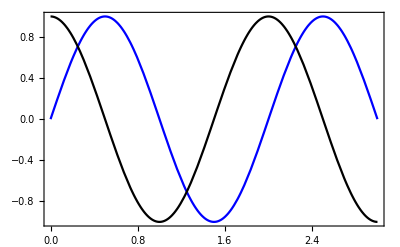

```mathematica
Plot[{Sin[Pi x],Cos[Pi x]},{x,0,3},PlotStyle->{Blue,Black}]
```

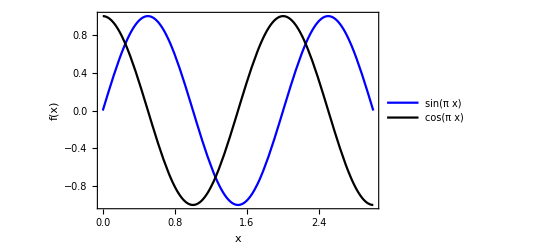

```mathematica
Plot[{Sin[Pi x],Cos[Pi x]},{x,0,3},PlotStyle->{Blue,Black},
FrameLabel->{"x","f(x)"},
PlotLegends->Placed["Expressions",Top]]
```

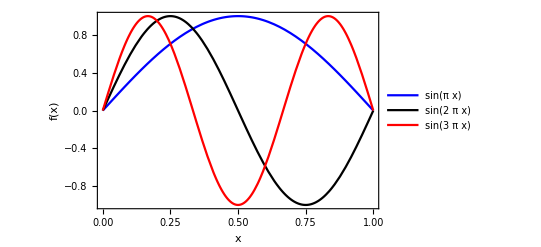

```mathematica
Plot[Evaluate@Table[Sin[n Pi x],{n,1,3}],{x,0,1},PlotStyle->{Blue,Black,Red},
FrameLabel->{"x","f(x)"},
PlotLegends->Placed["Expressions",Top]]
```

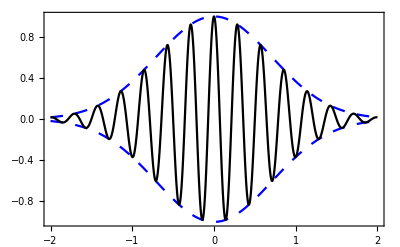

```mathematica
Plot[{Exp[-x^2],-Exp[-x^2],Exp[-x^2]Cos[7Pi x]},{x,-2,2},PlotStyle->{{Dashing[Medium],Blue},{Dashing[Medium],Blue},Black}]
```

## Plotting the solution of a damped harmonic oscillator

Suppose the equation of motion is y''+2y'+100y=0, and the initial conditions are y(0)=0, y'(0)=2.

### Use DSolve to solve the initial value problem

```mathematica
yOsc[t_]=y[t]/. DSolve[{y''[t]+2y'[t]+101y[t]==0,y[0]==0,y'[0]==2},y[t],t][[1]]
```

1/5 ⅇ^-t sin(10 t)

As expected, we see damped oscillations

### Plot the solution against time

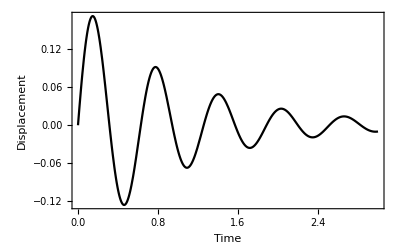

```mathematica
Plot[yOsc[t],{t,0,3},PlotStyle->Black,FrameLabel->{"Time","Displacement"}]
```

### Plot the solution along with the damping envelope

We’ll show the solution as a solid black line, and the exponential envelopes with dashed blue lines.

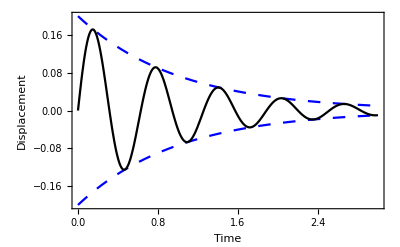

```mathematica
Plot[{Exp[-t]/5,-Exp[-t]/5,yOsc[t]},{t,0,3},PlotStyle->{{Dashing[Medium],Blue},{Dashing[Medium],Blue},Black},FrameLabel->{"Time","Displacement"}]
```